```mathematica
generateExpBarCharts[Variance_]:=Module[{centralIdealData,centralNoisyData,distrNoisyData,CIAvgs,CISDevs,CNAvgs,CNSDevs,DNAvgs,DNSDevs,makePlot,errorBar,chartData,CIData,CNData,DNData},
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}];
makePlot[data_,title_]:=BarChart[data,ChartElementFunction->errorBar["Rectangle"],PlotLabel->title,BarSpacing->{0,.5},ChartLabels->{{Framed["Cen. Ideal",FrameStyle->None,FrameMargins-> 20],Framed["Cen. Noisy",FrameStyle->None,FrameMargins-> 20],Framed["Distr. Noisy",FrameStyle->None,FrameMargins-> 20]}, None},ChartLegends-> Placed[{"Attempted","Failed"},Below],BaseStyle->FontSize->18,ImageSize-> {500,300}];

centralIdealData=<<("C:\\Users\\admin\\Documents\\Dropbox\\Grad School\\ActiveResearch\\static-exp-data\\Variance_"<>ToString[Variance]<>"_Data\\CentralIdealExpLog_ExpVariance_"<>ToString[Variance]<>".txt");
centralNoisyData=<<("C:\\Users\\admin\\Documents\\Dropbox\\Grad School\\ActiveResearch\\static-exp-data\\Variance_"<>ToString[Variance]<>"_Data\\CentralNoisyExpLog_ExpVariance_"<>ToString[Variance]<>".txt");
distrNoisyData=<<("C:\\Users\\admin\\Documents\\Dropbox\\Grad School\\ActiveResearch\\static-exp-data\\Variance_"<>ToString[Variance]<>"_Data\\DistrNoisyExpLog_ExpVariance_"<>ToString[Variance]<>".txt");

CIAvgs=Mean[centralIdealData⟦2;;101⟧];
CISDevs=StandardDeviation[centralIdealData⟦2;;101⟧];
CNAvgs=Mean[centralNoisyData⟦2;;101⟧];
CNSDevs=StandardDeviation[centralNoisyData⟦2;;101⟧];
DNAvgs=Mean[distrNoisyData⟦2;;101⟧];
DNSDevs=StandardDeviation[distrNoisyData⟦2;;101⟧];

CIData=Table[CIAvgs⟦i⟧->CISDevs⟦i⟧,{i,1,Length[CIAvgs]}];
CNData=Table[CNAvgs⟦i⟧->CNSDevs⟦i⟧,{i,1,Length[CNAvgs]}];
DNData=Table[DNAvgs⟦i⟧->DNSDevs⟦i⟧,{i,1,Length[DNAvgs]}];

Column[{
Grid[{{"Tasks","Attempted","Failed","Attempted %", "Failed %"},{"Cen. Ideal",N@CIAvgs⟦3⟧, N@CIAvgs⟦4⟧, CIAvgs⟦3⟧*100./5, CIAvgs⟦4⟧*100./CIAvgs⟦3⟧},{"Cen. Noisy",N@CNAvgs⟦3⟧,N@CNAvgs⟦4⟧, CNAvgs⟦3⟧*100./5,CNAvgs⟦4⟧*100./CNAvgs⟦3⟧},{"Distr. Noisy",N@DNAvgs⟦3⟧, N@DNAvgs⟦4⟧, DNAvgs⟦3⟧*100./5,DNAvgs⟦4⟧*100./DNAvgs⟦3⟧}}],
makePlot[{CIData⟦3;;4⟧,CNData⟦3;;4⟧,DNData⟦3;;4⟧},"Target Data (Central Noise σ="<>ToString[Variance]<>")"],
Grid[{{"Agents","Attempted","Failed","Attempted %", "Failed %"},{"Cen. Ideal",N@CIAvgs⟦5⟧, N@CIAvgs⟦6⟧,CIAvgs⟦5⟧*100./20, CIAvgs⟦6⟧*100./CIAvgs⟦5⟧},{"Cen. Noisy",N@CNAvgs⟦5⟧,N@CNAvgs⟦6⟧, CNAvgs⟦5⟧*100./20,CNAvgs⟦6⟧*100./CNAvgs⟦5⟧},{"Distr. Noisy",N@DNAvgs⟦5⟧, N@DNAvgs⟦6⟧,DNAvgs⟦5⟧*100./20, DNAvgs⟦6⟧*100./DNAvgs⟦5⟧}}],
makePlot[{CIData⟦5;;6⟧,CNData⟦5;;6⟧,DNData⟦5;;6⟧},"Agent Data (Central Noise σ="<>ToString[Variance]<>")"]
}]
]
```

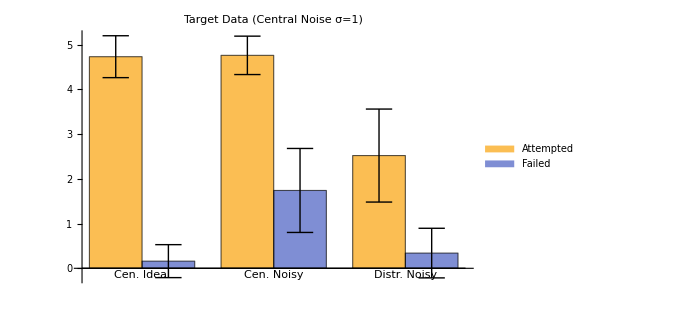
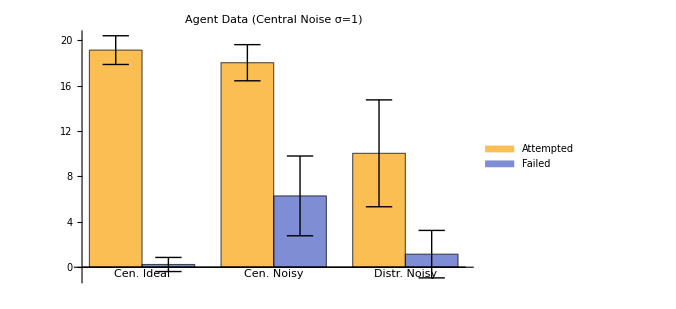
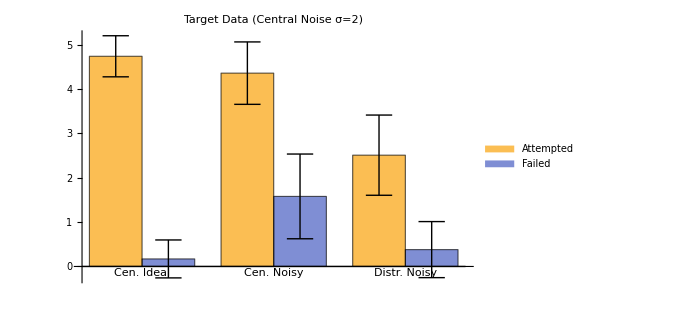
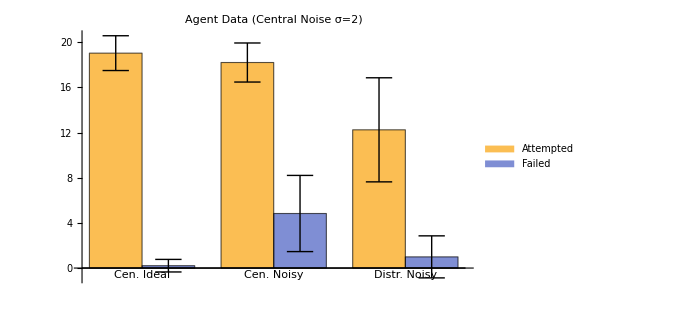
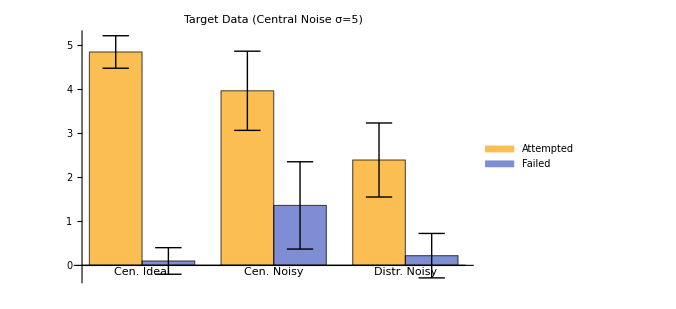
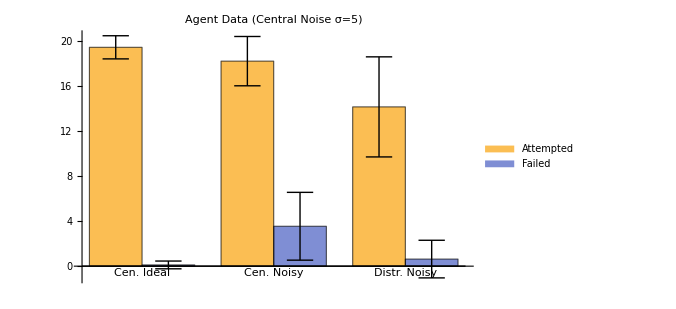
Tasks | Attempted | Failed | Attempted % | Failed %
Cen. Ideal | 4.73 | 0.16 | 94.6 | 3.38266
Cen. Noisy | 4.76 | 1.74 | 95.2 | 36.5546
Distr. Noisy | 2.52 | 0.34 | 50.4 | 13.4921
-Graphics-
Agents | Attempted | Failed | Attempted % | Failed %
Cen. Ideal | 19.12 | 0.24 | 95.6 | 1.25523
Cen. Noisy | 18.01 | 6.28 | 90.05 | 34.8695
Distr. Noisy | 10.03 | 1.15 | 50.15 | 11.4656
-Graphics-Tasks | Attempted | Failed | Attempted % | Failed %
Cen. Ideal | 4.74 | 0.17 | 94.8 | 3.5865
Cen. Noisy | 4.36 | 1.58 | 87.2 | 36.2385
Distr. Noisy | 2.51 | 0.38 | 50.2 | 15.1394
-Graphics-
Agents | Attempted | Failed | Attempted % | Failed %
Cen. Ideal | 19.03 | 0.21 | 95.15 | 1.10352
Cen. Noisy | 18.2 | 4.83 | 91. | 26.5385
Distr. Noisy | 12.24 | 0.99 | 61.2 | 8.08824
-Graphics-Tasks | Attempted | Failed | Attempted % | Failed %
Cen. Ideal | 4.84 | 0.1 | 96.8 | 2.06612
Cen. Noisy | 3.96 | 1.36 | 79.2 | 34.3434
Distr. Noisy | 2.39 | 0.22 | 47.8 | 9.20502
-Graphics-
Agents | Attempted | Failed | Attempted % | Failed %
Cen. Ideal | 19.47 | 0.11 | 97.35 | 0.564972
Cen. Noisy | 18.24 | 3.55 | 91.2 | 19.4627
Distr. Noisy | 14.17 | 0.63 | 70.85 | 4.44601
-Graphics-

```mathematica
Row[{generateExpBarCharts[1],generateExpBarCharts[2],generateExpBarCharts[5]}]
```